```mathematica
Import["~/Work/Documents_compartidos/pinguino.jpg"]
```

-Graphics-

#### MDEO: DM-DM annihilation to ν_Rν_R

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.11"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-9.9"]
<<FormCalc`
```

/home/anferivera/Work/FeynArts-3.11

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.11

/home/anferivera/Work/FormCalc-9.9

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

XX⟶Z'Z'

loading generic model file /home/anferivera/Work/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.11/Models/MDEOEWSB.mod

> 55 particles (incl. antiparticles) in 20 classes

> $CounterTerms are ON

> 151 vertices

classes model {MDEOEWSB} initialized

Excluding 0 Generic, 1 Classes, and 2 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

Restoring 0 Generic, 1 Classes, and 2 Particles fields

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

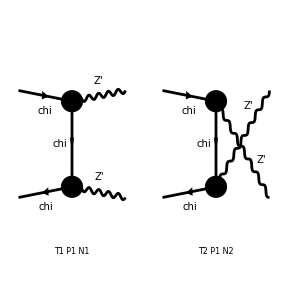

FeynArtsGraphics[{chi,chi}→{ComposedChar[Z'],ComposedChar[Z']}][([T1 P1 N1] | [T2 P1 N2] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
T2DM2F=CreateTopologies[0,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}];
(*Paint[T2DM2F];*)
n22=InsertFields[T2DM2F,{F[5],-F[5]}->{(*F[1],F[1]*)V[10],V[10]},InsertionLevel->{Particles},Model->"MDEOEWSB", GenericModel->"Lorentz", ExcludeParticles->{S[1]}];
Paint[n22]
```

#### Amplitude

```mathematica
resultn22=CalcFeynAmp[CreateFeynAmp[n22],FermionChains->VA,Antisymmetrize->False,Invariants->True(*,Normalized->True*)];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

preparing FORM code in /home/anferivera/Work/FormCalc-9.9/fc-amp-4.frm

running FORM...

ok

For doublet DM (We obtain the same result)

```mathematica
Den[x_,y_]:= 1/(x-y) 
expr1=Simplify[ComplexExpand[ Plus@@resultn22//.Subexpr[]//.Abbr[]]//.MassChi->Mx/.{CTWp->1,STWp->0}]
```

1/(2 (Mx^2-T) (Mx^2-U))gBL^2 (-Mx (Mx^2-T) Mat[<v1|1,ec[3],ec[4]|u2>]+Mx (Mx^2-U) Mat[<v1|1,ec[3],ec[4]|u2>]-19 Mx (Mx^2-T) Mat[<v1|5,ec[3],ec[4]|u2>]-19 Mx (Mx^2-U) Mat[<v1|5,ec[3],ec[4]|u2>]+181 (Mx^2-T) Mat[<v1|1,ec[3],ec[4],k[3]|u2>]+181 (Mx^2-U) Mat[<v1|1,ec[3],ec[4],k[3]|u2>]+19 (Mx^2-T) Mat[<v1|5,ec[3],ec[4],k[3]|u2>]+19 (Mx^2-U) Mat[<v1|5,ec[3],ec[4],k[3]|u2>]+2 Mx (Mx^2-T) Mat[<v1|1|u2>] Pair[ec[3],ec[4]]+38 Mx (Mx^2-T) Mat[<v1|5|u2>] Pair[ec[3],ec[4]]-362 (Mx^2-T) Mat[<v1|1,k[3]|u2>] Pair[ec[3],ec[4]]-38 (Mx^2-T) Mat[<v1|5,k[3]|u2>] Pair[ec[3],ec[4]]+362 (Mx^2-U) Mat[<v1|1,ec[4]|u2>] Pair[ec[3],k[1]]+38 (Mx^2-U) Mat[<v1|5,ec[4]|u2>] Pair[ec[3],k[1]]-362 (Mx^2-T) Mat[<v1|1,ec[4]|u2>] Pair[ec[3],k[2]]-38 (Mx^2-T) Mat[<v1|5,ec[4]|u2>] Pair[ec[3],k[2]]-362 (Mx^2-U) Mat[<v1|1,ec[3]|u2>] Pair[ec[4],k[3]]-38 (Mx^2-U) Mat[<v1|5,ec[3]|u2>] Pair[ec[4],k[3]])

```mathematica
(*expr1=Simplify[kk/.{T-MassXi[2]^2->1/rr,-T+MassXi[2]^2->1/rr,U-MassXi[2]^2->1/rr,-U+MassXi[2]^2->1/rr,T-MassXi[3]^2->1/rr,U-MassXi[3]^2->1/rr,-T+MassXi[3]^2->1/rr,-U+MassXi[3]^2->1/rr}/.rr->0/.MassXi[1]->Mx]*)
```

For singlet DM

#### Check divergences

```mathematica
uvcheck=UVDivergentPart[expr1]//Simplify
FreeQ[uvcheck,Divergence]
```

0

True

#### Momentum in the computation

Conservation of the energy-momentum

```mathematica
(*k1={E1,p1,0,0};
k2={E1,-p1,0,0}; 
k3={E1,p3*ct,p3*st,0};(*duda*)
k4={E1,-p3*ct,-p3*st,0};
e0={1,0,0,0};(* See the Lahiri and Palash book*)
e1={0,1,0,0};
e2={0,0,1,0};
e3={0,0,0,1};
emu={e0,e1,e2,e3};*)

k1={E1,0,p1*st,p1*ct}; (*Halzen and Martin book*)
k2={E1,0,-p1*st,-p1*ct}; 
k3={E1,0,0,p3};
k4={E1,0,0,-p3};
(* Polarization vector conjugated*)
(*e1={0,1,-I,0}/Sqrt[2];(* See the Lahiri and Palash book*)
e2={0,1,I,0}/Sqrt[2];
e3={p3,0,0,E1}/MZp;*)
e1={0,1,0,0};
e2={0,0,1,0};
e3={0,0,0,1};
```

#### Mandelstan variables

```mathematica
guv={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   T->(k1 - k3).guv.(k1 - k3),   U ->(k1 - k4).guv.(k1 - k4)}];
MV // MatrixForm
```

(S→4 E1^2
T→-(-ct p1+p3)^2-p1^2 st^2
U→-(ct p1+p3)^2-p1^2 st^2)

#### Pairs and Dirac Chains

```mathematica
InputForm[expr1]
```

(gBL^2*(121*Mx*(T - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[3], ec[4], Spinor[k[2], Mx, 1]]] + 11*Mx*(2*Mx^2 - T - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[3], ec[4], Spinor[k[2], Mx, 1]]] + 61*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[3], ec[4], k[3], Spinor[k[2], Mx, 1]]] + 
   61*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[3], ec[4], k[3], Spinor[k[2], Mx, 1]]] - 11*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[3], ec[4], k[3], Spinor[k[2], Mx, 1]]] - 11*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[3], ec[4], k[3], Spinor[k[2], Mx, 1]]] + 
   242*Mx*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, Spinor[k[2], Mx, 1]]]*Pair[ec[3], ec[4]] - 22*Mx*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, Spinor[k[2], Mx, 1]]]*Pair[ec[3], ec[4]] - 122*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, k[3], Spinor[k[2], Mx, 1]]]*Pair[ec[3], ec[4]] + 
   22*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, k[3], Spinor[k[2], Mx, 1]]]*Pair[ec[3], ec[4]] + 122*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[4], Spinor[k[2], Mx, 1]]]*Pair[ec[3], k[1]] - 22*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[4], Spinor[k[2], Mx, 1]]]*Pair[ec[3], k[1]] - 
   122*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[4], Spinor[k[2], Mx, 1]]]*Pair[ec[3], k[2]] + 22*(Mx^2 - T)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[4], Spinor[k[2], Mx, 1]]]*Pair[ec[3], k[2]] - 122*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 1, ec[3], Spinor[k[2], Mx, 1]]]*Pair[ec[4], k[3]] + 
   22*(Mx^2 - U)*Mat[DiracChain[Spinor[k[1], Mx, -1], 5, ec[3], Spinor[k[2], Mx, 1]]]*Pair[ec[4], k[3]]))/(2*(Mx^2 - T)*(Mx^2 - U))

```mathematica
Simplify[expr1/.{ Pair[ec[3],ec[4]]->0,Pair[ec[3],k[1]]->0,Pair[ec[3],k[2]]->0,Pair[ec[3],k[3]]->0,Pair[ec[4],k[3]]->0}]
```

-((CTWp gBL+gYB STW STWp)^2 (Mx (-T+U) Mat[<v1|1,ec[3],ec[4]|u2>]+(2 Mx^2-T-U) (19 Mx Mat[<v1|5,ec[3],ec[4]|u2>]-181 Mat[<v1|1,ec[3],ec[4],k[3]|u2>]-19 Mat[<v1|5,ec[3],ec[4],k[3]|u2>])))/(2 (Mx^2-T) (Mx^2-U))

```mathematica
kk=InputForm[expr1/.{
Mat[DiracChain[Spinor[k[1],Mx,-1],1,Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],1,k[3],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,k[3],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[4],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[4],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],ec[4],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],ec[4],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],ec[4],k[3],Spinor[k[2],Mx,1]]]->0,
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],ec[4],k[3],Spinor[k[2],Mx,1]]]->0}/.MV//. st^2->(1- ct^2)]
```

0

## Dirac spinors.

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3};

χ[s_]:=If[s==1,{1,0},{0,1}]
```

Spinors (Cheng appendix)

```mathematica
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+Mx));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+Mx));
```

χ1 | χ2
(1
0) | (0
1)

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp1,Mx,k1[[1]]]//MatrixForm

vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp1,Mx,k1[[1]]]//MatrixForm
```

(√(E1+Mx)
0
(ct p1)/(√(E1+Mx))
(ⅈ p1 st)/(√(E1+Mx)))

((ct p1)/(√(E1+Mx))
(ⅈ p1 st)/(√(E1+Mx))
√(E1+Mx)
0)

Check

```mathematica
e3
```

{p3/MZp,0,0,E1/MZp}

```mathematica
gamma3
```

{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}}

```mathematica
e2.guv.gammamu//MatrixForm
```

(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,Mx,k1[[1]]]]).gamma0.uspinor[1,σp1,Mx,k1[[1]]]/.{S->4E1^2}],Element[{E1,Mx,√(E1+Mx),1/(√(E1+Mx)),p1,ct,st},Reals] ]/.{p1^2-> E1^2-Mx^2,st^2->(1- ct^2)}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,Mx,k2[[1]]]]).gamma0.uspinor[1,σp2,Mx,k2[[1]]]/.{S->4E1^2}],Element[{E1,Mx,√(E1+Mx),1/(√(E1+Mx)),p1,ct,st},Reals] ]/.{p1^2-> E1^2-Mx^2,st^2->(1- ct^2)}]
```

2 Mx

2 Mx

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,Mx,k1[[1]]]]).gamma0.vspinor[1,σp1,Mx,k1[[1]]]],Element[{E1,Mx,√(E1+Mx),1/(√(E1+Mx)),p1,ct,st},Reals] ]/.{p1^2-> E1^2-Mx^2,st^2->(1- ct^2)}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Mx,k2[[1]]]]).gamma0.vspinor[1,σp2,Mx,k2[[1]]]],Element[{E1,Mx,√(E1+Mx),1/(√(E1+Mx)),p1,ct,st},Reals] ]/.{p1^2-> E1^2-Mx^2,st^2->(1- ct^2)}]
```

-2 Mx

-2 Mx

```mathematica
AMP[s1_,s2_,ep3_,ep4_]:=
expr1//.{
Mat[DiracChain[Spinor[k[1],Mx,-1],1,Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],1,k[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.(k3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,k[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.(k3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.(ep3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.(ep3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[4],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.(ep4.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[4],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.(ep4.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],ec[4],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.(ep3.guv.gammamu).(ep4.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],ec[4],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.(ep3.guv.gammamu).(ep4.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],1,ec[3],ec[4],k[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.(ep3.guv.gammamu).(ep4.guv.gammamu).(k3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Mat[DiracChain[Spinor[k[1],Mx,-1],5,ec[3],ec[4],k[3],Spinor[k[2],Mx,1]]]->Conjugate[vspinor[s1,σp1,Mx,k1[[1]]]].gamma0.gamma5.(ep3.guv.gammamu).(ep4.guv.gammamu).(k3.guv.gammamu).uspinor[s2,σp2,Mx,k2[[1]]],
Pair[ec[3],ec[4]]->ep3.guv.ep4,
Pair[ec[3],k[1]]->ep3.guv.k1,
Pair[ec[3],k[2]]->ep3.guv.k2,
Pair[ec[3],k[3]]->ep3.guv.k3,
Pair[ec[4],k[3]]->ep4.guv.k3
}
```

```mathematica
AMP=Simplify[Sum[AMP[s1,s2,ep3,ep4],{s1,{-1,1}},{s2,{-1,1}},{ep3,{e1,e2,e3}},{ep4,{e1,e2,e3}}],Element[{p1,p3,E1,√(E1+Mx),1/(√(E1+Mx)),ct,st},Reals]]
```

1/((E1+Mx) (Mx^2-T) (Mx^2-U))gBL^2 (-362 Mx^4 p3+724 Mx^4 p1 st+76 ⅈ Mx^3 p1 p3 st-152 ⅈ Mx^3 p1^2 st^2-362 Mx^2 p1^2 p3 st^2+724 Mx^2 p1^3 st^3-57 Mx^3 T-362 Mx^2 p1 st T-114 ⅈ Mx p1 p3 st T-(57-76 ⅈ) Mx p1^2 st^2 T-362 p1^3 st^3 T+362 ct^3 p1^3 (2 Mx^2-T-U)+57 E1^3 (T-U)+57 Mx^3 U+362 Mx^2 p3 U-362 Mx^2 p1 st U+38 ⅈ Mx p1 p3 st U+(57+76 ⅈ) Mx p1^2 st^2 U+362 p1^2 p3 st^2 U-362 p1^3 st^3 U+2 ct p1 (362 Mx^4-38 ⅈ Mx^3 p3+181 E1^2 (2 Mx^2-T-U)+181 Mx^2 (2 p1^2 st^2-T-U)+38 ⅈ Mx p3 U-181 p1^2 st^2 (T+U)+E1 (724 Mx^3-38 ⅈ Mx^2 p3+38 ⅈ p3 U-362 Mx (T+U)))+ct^2 p1^2 (152 ⅈ Mx^3-362 Mx^2 (p3-2 p1 st)+19 ⅈ E1 (8 Mx^2-(4-3 ⅈ) T-(4+3 ⅈ) U)-19 Mx ((3+4 ⅈ) T-(3-4 ⅈ) U)-362 (-p3 U+p1 st (T+U)))+E1^2 (-362 Mx^2 (p3-2 p1 st)+57 Mx (T-U)-362 (-p3 U+p1 st (T+U)))+E1 (-724 Mx^3 (p3-2 p1 st)+19 Mx^2 (4 ⅈ p1 p3 st-8 ⅈ p1^2 st^2-3 T+3 U)+19 ⅈ p1 st (-6 p3 T+(4+3 ⅈ) p1 st T+2 p3 U+(4-3 ⅈ) p1 st U)-724 Mx (-p3 U+p1 st (T+U))))

#### Phase space factor

```mathematica
cinematic={E1->√((p1)^2+Mx^2),p3->√((p1)^2+Mx^2-MZp^2),p1->Mx*v*(1+0*v^2/2)}; (*relativistic p1*)
```

```mathematica
F1=Simplify[(1/(64*π^2*S)*√(((S-(MZp+MZp)^2)(S-(MZp-MZp)^2))/((S-(Mx+Mx)^2)(S-(Mx-Mx)^2))))/.MV//.cinematic]
```

(√(1+(1-MZp^2/Mx^2)/v^2))/(256 Mx^2 π^2 (1+v^2))

```mathematica
F2=Normal[Series[F1,{v,0,2}]]
```

(√(1-MZp^2/Mx^2))/(256 Mx^2 π^2 v)+((-Mx^2+2 MZp^2) v)/(512 Mx^4 √((Mx^2-MZp^2)/Mx^2) π^2)

#### Amplitude squared

```mathematica
F3=Simplify[(AMP*Conjugate[AMP])/.MV//. st^2->(1- ct^2),Element[{p1,p3,E1,Mx,MZp,ct,st,gBL,gYB},Reals]]
```

1/((E1+Mx)^2 (Mx^2+p1^2-2 ct p1 p3+p3^2)^2 (Mx^2+p1^2+2 ct p1 p3+p3^2)^2)4 gBL^4 (-76 ⅈ Mx^3 p1^2-76 ⅈ Mx p1^4-181 Mx^4 p3-362 Mx^2 p1^2 p3-114 ct^3 E1 p1^3 p3-181 p1^4 p3-76 ⅈ Mx p1^2 p3^2-181 Mx^2 p3^3-181 p1^2 p3^3+362 Mx^4 p1 st+362 Mx^2 p1^3 st+38 ⅈ Mx^3 p1 p3 st+38 ⅈ Mx p1^3 p3 st+362 Mx^2 p1 p3^2 st+38 ⅈ Mx p1 p3^3 st+362 Mx^2 p1^3 st^3+362 p1^5 st^3+362 p1^3 p3^2 st^3-181 E1^2 (Mx^2+p1^2+p3^2) (p3-2 p1 st)+2 ct^2 p1^2 (76 ⅈ Mx^3+38 ⅈ E1 (2 Mx^2+p1^2)+38 ⅈ Mx (2 p1^2+p3^2)+181 Mx^2 p1 st+181 p1 (p1^2+p3^2) st)+E1 (-362 Mx^3 (p3-2 p1 st)+362 Mx (p1^2+p3^2) (-p3+2 p1 st)-38 ⅈ p1 (p1^2+p3^2) st (-p3+2 p1 st)-38 ⅈ Mx^2 p1 (2 p1-p3 st))+2 ct p1 (181 Mx^4+362 Mx^2 p1^2+181 p1^4+57 E1^3 p3-(57+19 ⅈ) Mx^3 p3+E1^2 (181 Mx^2+181 p1^2+57 Mx p3)-19 ⅈ Mx p3 ((1-3 ⅈ) p1^2+p3^2+4 p1 p3 st)+E1 (362 Mx^3+362 Mx p1^2-(57+19 ⅈ) Mx^2 p3-19 ⅈ p3 (p1^2+p3^2+4 p1 p3 st-3 ⅈ p1^2 st^2)))) (2 ct^3 p1^3 (181 Mx^2+181 p1^2-57 E1 p3-57 Mx p3)+(Mx^2+p1^2+p3^2) (-p3+2 p1 st) (181 E1^2+362 E1 Mx+181 Mx^2+38 ⅈ E1 p1 st+38 ⅈ Mx p1 st+181 p1^2 st^2)+ct^2 p1^2 (-76 ⅈ Mx^3-76 ⅈ Mx p1^2-76 ⅈ E1 (Mx^2+p1^2)-181 Mx^2 (p3-2 p1 st)+181 (p1^2+p3^2) (-p3+2 p1 st))+2 ct p1 (181 Mx^4+57 E1^3 p3-(57-19 ⅈ) Mx^3 p3+E1^2 (181 Mx^2+181 p1^2+57 Mx p3)+181 p1^4 st^2+181 Mx^2 p1^2 (1+st^2)+19 ⅈ Mx p3 (p1^2+p3^2+4 p1 p3 st+3 ⅈ p1^2 st^2)+E1 (362 Mx^3+362 Mx p1^2-(57-19 ⅈ) Mx^2 p3+19 ⅈ p3 (p1^2+p3^2+4 p1 p3 st+3 ⅈ p1^2 st^2))))

```mathematica
F4=Simplify[F3//.cinematic,Mx>0]
```

(8 gBL^4 Mx (Mx (-MZp^2+2 Mx^2 (1+v^2)) (181 st^2 v^2+38 ⅈ st v (1+√(1+v^2))+181 (2+v^2+2 √(1+v^2))) (2 Mx st v-√(-MZp^2+Mx^2 (1+v^2)))-2 ct^3 Mx^3 v^3 (-181 Mx (1+v^2)+57 (1+√(1+v^2)) √(-MZp^2+Mx^2 (1+v^2)))-ct^2 Mx v^2 (362 Mx MZp^2 st v-181 MZp^2 √(-MZp^2+Mx^2 (1+v^2))+362 Mx^2 (1+v^2) √(-MZp^2+Mx^2 (1+v^2))+4 ⅈ Mx^3 (1+v^2) (181 ⅈ st v+19 (1+√(1+v^2))))+2 ct Mx v (-76 ⅈ Mx MZp^2 st v (1+√(1+v^2))-19 ⅈ MZp^2 (1+√(1+v^2)) √(-MZp^2+Mx^2 (1+v^2))-19 Mx^2 (-2 ⅈ+((-3-2 ⅈ)+3 st^2) v^2) (1+√(1+v^2)) √(-MZp^2+Mx^2 (1+v^2))+Mx^3 (1+v^2) (181 st^2 v^2+76 ⅈ st v (1+√(1+v^2))+181 (2+v^2+2 √(1+v^2))))) (-57 ct^3 Mx^2 v^3 √(1+v^2) √(-MZp^2+Mx^2 (1+v^2))+MZp^2 √(-MZp^2+Mx^2 (1+v^2)) (-19 ⅈ st v (1+√(1+v^2))+181 (1+v^2+√(1+v^2)))-2 Mx^2 (1+v^2) √(-MZp^2+Mx^2 (1+v^2)) (-19 ⅈ st v (1+√(1+v^2))+181 (1+v^2+√(1+v^2)))-Mx MZp^2 v (-38 ⅈ v+181 st^3 v^2-38 ⅈ st^2 v √(1+v^2)+181 st (2+v^2+2 √(1+v^2)))+2 Mx^3 v (-19 ⅈ st^2 v √(1+v^2) (1+2 v^2)+181 st^3 (v^2+v^4)-19 ⅈ v (2+2 v^2+√(1+v^2))+181 st (1+v^2) (2+v^2+2 √(1+v^2)))+ct v (76 ⅈ Mx MZp^2 st v (1+√(1+v^2))+19 ⅈ MZp^2 (1+√(1+v^2)) √(-MZp^2+Mx^2 (1+v^2))+2 Mx^3 (1+v^2) (-38 ⅈ st v (1+√(1+v^2))+181 (1+v^2+√(1+v^2)))-19 Mx^2 √(-MZp^2+Mx^2 (1+v^2)) (2 ⅈ (1+√(1+v^2))+v^2 (2 ⅈ-(3-2 ⅈ) √(1+v^2)+3 st^2 √(1+v^2))))+ct^2 Mx v^2 (-MZp^2 (38 ⅈ+181 st v)+2 Mx^2 (181 st (v+v^3)+19 ⅈ (3+2 √(1+v^2)+v^2 (3+√(1+v^2)))))))/((1+√(1+v^2))^2 (MZp^2-2 Mx^2 (1+v^2)-2 ct Mx v √(-MZp^2+Mx^2 (1+v^2)))^2 (MZp^2-2 Mx^2 (1+v^2)+2 ct Mx v √(-MZp^2+Mx^2 (1+v^2)))^2)

```mathematica
F5=Collect[Normal[Series[F4,{v,0,2}]],{v,v^2}]
```

(524176 gBL^4 Mx^2 (Mx^2-MZp^2))/((2 Mx^2-MZp^2)^2)-(2096704 gBL^4 Mx^3 (ct Mx^2 √(Mx^2-MZp^2)+2 Mx^2 √(Mx^2-MZp^2) st-MZp^2 √(Mx^2-MZp^2) st) v)/((2 Mx^2-MZp^2)^3)+1/((2 Mx^2-MZp^2)^4)4 gBL^4 Mx^2 (-131044 Mx^6+1709348 ct^2 Mx^6+262088 Mx^4 MZp^2-2370344 ct^2 Mx^4 MZp^2+98283 Mx^2 MZp^4+1219377 ct^2 Mx^2 MZp^4-98283 MZp^6-34205 ct^2 MZp^6+82536 ⅈ Mx^5 √(Mx^2-MZp^2)-82536 ⅈ ct^2 Mx^5 √(Mx^2-MZp^2)-68780 ⅈ Mx^3 MZp^2 √(Mx^2-MZp^2)+68780 ⅈ ct^2 Mx^3 MZp^2 √(Mx^2-MZp^2)+13756 ⅈ Mx MZp^4 √(Mx^2-MZp^2)-13756 ⅈ ct^2 Mx MZp^4 √(Mx^2-MZp^2)+2085152 ct Mx^6 st-1025248 ct Mx^4 MZp^2 st-14440 ct Mx^2 MZp^4 st+2888 ct MZp^6 st+2233524 Mx^6 st^2-2370344 Mx^4 MZp^2 st^2+695201 Mx^2 MZp^4 st^2-34205 MZp^6 st^2-82536 ⅈ Mx^5 √(Mx^2-MZp^2) st^2+68780 ⅈ Mx^3 MZp^2 √(Mx^2-MZp^2) st^2-13756 ⅈ Mx MZp^4 √(Mx^2-MZp^2) st^2) v^2

```mathematica
F6=Simplify[F5/.v->0]
```

(524176 gBL^4 Mx^2 (Mx^2-MZp^2))/((-2 Mx^2+MZp^2)^2)

#### dσ/dΩ

```mathematica
F7=Simplify[F2*F6]
```

-(32761 gBL^4 √(1-MZp^2/Mx^2) (Mx^2 (-2+v^2)-2 MZp^2 (-1+v^2)))/(32 (-2 Mx^2+MZp^2)^2 π^2 v)

#### σ(v)=∫ (dσ/dΩ)dΩ

```mathematica
Integrate[((F7*2Pi*Sin[t])//.{st->Sin[t],ct->Cos[t]}),{t,0,Pi}];
sigma=Normal[Series[%,{v,0,2}]]
```

-(32761 gBL^4 (-2 Mx^2+2 MZp^2) √(1-MZp^2/Mx^2))/(8 (-2 Mx^2+MZp^2)^2 π v)-(32761 gBL^4 (Mx^2-2 MZp^2) √(1-MZp^2/Mx^2) v)/(8 (-2 Mx^2+MZp^2)^2 π)

#### σ .vr

We averaged in the initial spin and the final polarization photons: also we take care of two indistinguishable particles in the final state

```mathematica
sigmavr=Collect[((1/4*1/1*1/2)*(sigma*v)/.v->(vr/2)),{vr,vr^2}]
```

-(32761 gBL^4 (-2 Mx^2+2 MZp^2) √(1-MZp^2/Mx^2))/(64 (-2 Mx^2+MZp^2)^2 π)-(32761 gBL^4 (Mx^2-2 MZp^2) √(1-MZp^2/Mx^2) vr^2)/(256 (-2 Mx^2+MZp^2)^2 π)

#### S - wave part

```mathematica
F8= Simplify[sigmavr/.vr->0]
```

(32761 gBL^4 (Mx^2-MZp^2) √(1-MZp^2/Mx^2))/(32 (-2 Mx^2+MZp^2)^2 π)

```mathematica
Simplify[F8/.MZp->r*Mx,Mx>0]
```

(32761 gBL^4 (1-r^2)^(3/2))/(32 Mx^2 π (-2+r^2)^2)

```mathematica
N[32761/(32*4*9)]
```

28.4384

#### P - wave part

```mathematica
F9=Simplify[D[D[sigmavr,vr],vr]/2/.vr->0]
```

-(32761 gBL^4 (Mx^2-2 MZp^2) √(1-MZp^2/Mx^2))/(256 (-2 Mx^2+MZp^2)^2 π)

```mathematica
F9=Simplify[D[D[sigmavr,vr]/2,vr]/.vr->0]
```

-(32761 gBL^4 (Mx^2-2 MZp^2) √(1-MZp^2/Mx^2))/(256 (-2 Mx^2+MZp^2)^2 π)

```mathematica
Simplify[F9/.MZp->r*Mx,Mx>0]
```

(32761 gBL^4 √(1-r^2) (-1+2 r^2))/(256 Mx^2 π (-2+r^2)^2)

```mathematica
N[361/96]
```

3.76042

```mathematica
96/16
```

6